## Parámetros comunes

```mathematica
ColoresTema=ColorData[106,"ColorList"];
CIS=450; (*Tamaño de imagen comun*)
CLS=45;
```

## Gráficas de Datos Obtenidos

```mathematica
Folder="C:\\Users\\Rodrigo\\Desktop\\Tesis\\DAQ\\Datos_Para_Entrenamiento\\";
SetDirectory[Folder];
Run["dir /b > filename.txt"];
Files=Import["filename.txt","List"];
SetVsDP={{"Nombre","Número de Datos"}};
SetVsMFP={{"Nombre","Aptitud Maxima Posible"}};
```

```mathematica
For[i=1,i<=Length[Files],i++,
If[StringCount[Files[[i]],".csv"]>0,
Data=Import[Files[[i]],"Data"];
InData=Data[[;;,1;;2]];
OutData=Data[[;;,1;;3;;2]];
MAXFitness=Sum[Abs[OutData[[j,2]]],{j,Length[OutData]}];
(*Print[ListLinePlot[{InData,OutData},PlotRange->Full,PlotLabel->Files[[i]],PlotLegends->{"Voltaje de Entrada","Posición de Salida"}]];*)

SetVsDP=Join[SetVsDP,{{StringReplace[Files[[i]],".csv"->""],Length[InData]}}];
SetVsMFP=Join[SetVsMFP,{{StringReplace[Files[[i]],".csv"->""],MAXFitness}}];

InPlot=ListLinePlot[InData,
PlotRange->All,
PlotLabel->Files[[i]],
Axes->False,
Frame->{False,False,False,True},
ImagePadding->50,
FrameTicks->{{None,All},{None,None}},
PlotStyle->ColoresTema[[2]],
FrameLabel->{{"","Voltaje [V]"},{"",""}},
FrameStyle->{{Automatic,ColoresTema[[2]]},{Automatic,Automatic}},
ImageSize->Large];

OutPlot=ListLinePlot[OutData,
PlotRange->All,
Axes->False,
Frame->{True,True,True,False},
ImagePadding->50,
FrameTicks->All,
PlotStyle->ColoresTema[[1]],
FrameLabel->{"Tiempo[s]","Posición [rad]"},
FrameStyle->{Automatic,ColoresTema[[1]],Automatic,Automatic},
ImageSize->Large];

Imagen=Overlay[{InPlot,OutPlot},Alignment->{0,-1},ImageSize->Full];
(*Export[Folder<>"Graficas\\"<>"Grafica_"<>StringReplace[Files[[i]],".csv"->""]<>".eps",Imagen]*)
(*Print[Imagen];*)
]
]
```

```mathematica
Row[{SetVsDP//MatrixForm,
SetVsMFP//MatrixForm}]
Union[SetVsDP,SetVsMFP]//MatrixForm
```

(Nombre | Número de Datos
Chirp_1 | 10000
Chirp_2 | 10000
Chirp_3 | 10000
Chirp_4 | 10000
Chirp_5 | 10000
Chirp_mr_1 | 1000
Chirp_mr_2 | 1000
Chirp_mr_3 | 1000
Chirp_mr_4 | 1000
Chirp_mr_5 | 1000
Impulso_1 | 1000
PRB_1 | 10000
PRB_10 | 10000
PRB_2 | 10000
PRB_3 | 10000
PRB_4 | 10000
PRB_5 | 10000
PRB_6 | 10000
PRB_7 | 10000
PRB_8 | 10000
PRB_9 | 10000
PRB_mr_1 | 1000
PRB_mr_2 | 1000
tj_Chirp_2 | 4984
tj_Chirp_mr_1 | 491
tj_Chirp_mr_2 | 493
tj_Chirp_mr_3 | 479
tj_PRB_2 | 4938)(Nombre | Aptitud Maxima Posible
Chirp_1 | 1.56826×10^6
Chirp_2 | 4.18933×10^6
Chirp_3 | 7.14452×10^6
Chirp_4 | 1.0091×10^7
Chirp_5 | 1.30308×10^7
Chirp_mr_1 | 177982.
Chirp_mr_2 | 442454.
Chirp_mr_3 | 1.03534×10^6
Chirp_mr_4 | 739858.
Chirp_mr_5 | 1.32938×10^6
Impulso_1 | 21754.9
PRB_1 | 3.72325×10^6
PRB_10 | 2.86989×10^7
PRB_2 | 1.08804×10^7
PRB_3 | 1.81344×10^7
PRB_4 | 2.53661×10^7
PRB_5 | 3.25879×10^7
PRB_6 | 6.12366×10^6
PRB_7 | 1.19566×10^7
PRB_8 | 1.7528×10^7
PRB_9 | 2.31055×10^7
PRB_mr_1 | 421198.
PRB_mr_2 | 1.06324×10^6
tj_Chirp_2 | 2.09176×10^6
tj_Chirp_mr_1 | 89025.
tj_Chirp_mr_2 | 221211.
tj_Chirp_mr_3 | 496486.
tj_PRB_2 | 5.3694×10^6)

(Chirp_1 | 10000
Chirp_1 | 1.56826×10^6
Chirp_2 | 10000
Chirp_2 | 4.18933×10^6
Chirp_3 | 10000
Chirp_3 | 7.14452×10^6
Chirp_4 | 10000
Chirp_4 | 1.0091×10^7
Chirp_5 | 10000
Chirp_5 | 1.30308×10^7
Chirp_mr_1 | 1000
Chirp_mr_1 | 177982.
Chirp_mr_2 | 1000
Chirp_mr_2 | 442454.
Chirp_mr_3 | 1000
Chirp_mr_3 | 1.03534×10^6
Chirp_mr_4 | 1000
Chirp_mr_4 | 739858.
Chirp_mr_5 | 1000
Chirp_mr_5 | 1.32938×10^6
Impulso_1 | 1000
Impulso_1 | 21754.9
Nombre | Aptitud Maxima Posible
Nombre | Número de Datos
PRB_1 | 10000
PRB_1 | 3.72325×10^6
PRB_10 | 10000
PRB_10 | 2.86989×10^7
PRB_2 | 10000
PRB_2 | 1.08804×10^7
PRB_3 | 10000
PRB_3 | 1.81344×10^7
PRB_4 | 10000
PRB_4 | 2.53661×10^7
PRB_5 | 10000
PRB_5 | 3.25879×10^7
PRB_6 | 10000
PRB_6 | 6.12366×10^6
PRB_7 | 10000
PRB_7 | 1.19566×10^7
PRB_8 | 10000
PRB_8 | 1.7528×10^7
PRB_9 | 10000
PRB_9 | 2.31055×10^7
PRB_mr_1 | 1000
PRB_mr_1 | 421198.
PRB_mr_2 | 1000
PRB_mr_2 | 1.06324×10^6
tj_Chirp_2 | 4984
tj_Chirp_2 | 2.09176×10^6
tj_Chirp_mr_1 | 491
tj_Chirp_mr_1 | 89025.
tj_Chirp_mr_2 | 493
tj_Chirp_mr_2 | 221211.
tj_Chirp_mr_3 | 479
tj_Chirp_mr_3 | 496486.
tj_PRB_2 | 4938
tj_PRB_2 | 5.3694×10^6)

## Gráficas del Registro (Log)

```mathematica
Folder="C:\\Users\\Rodrigo\\Desktop\\Tesis\\DAQ\\Datos_Para_Entrenamiento\\Logs\\";
SetDirectory[Folder];
Run["dir /b > filename.txt"];
Files=Import["filename.txt","List"];
GenVsSet={{"File","Total Generations"}};
For[i=1,i!=Length[Files],i++,
If[StringCount[Files[[i]],".log"]==0,
Files=Delete[Files,i];
i--;
]
]
Files=StringReplace[Files,".log"->""];
Trainings=StringReplace[Files,Join[Table[ToString[i]<>"_"->ToString[i]<>", ",{i,1,10}],{"_"->" "}]];
(*Trainings=Table[StringDrop[StringDrop[Trainings[[i]],-2],1],{i,Length[Trainings]}];*)
Trainings=Table[StringDrop[StringDrop[Trainings[[i]],{StringPosition[Trainings[[i]],","][[-1,-1]]}],1],{i,Length[Trainings]}];
Trainings=Join[{"Entrenamiento"},Trainings];
Files=Join[{"Entrenamiento"},Files];
```

```mathematica
MaxFitnessPosible={" Aptitud máxima posible "};
TotalDataPoints={" Datos totales "};
NGen={" Generaciones "};
BestFitness={" Aptitud "};

For[i=2,i<=Length[Files],i++,

MaxFitnessPosible=Join[MaxFitnessPosible,{Sum[2SetVsMFP[[l,2]]StringCount[Files[[i]],SetVsMFP[[l,1]]],{l,2,Length[SetVsMFP]}]}];
TotalDataPoints=Join[TotalDataPoints,{Sum[SetVsDP[[l,2]]StringCount[Files[[i]],SetVsDP[[l,1]]],{l,2,Length[SetVsDP]}]}];

Data=Import[Files[[i]]<>".log","Data"];
TotalT=DateObject[Data[[-2,1]]]-DateObject[Data[[1,1]]];
TotalT=ToString[UnitConvert[TotalT,MixedRadix["Hours","Minutes","Seconds"]],StandardForm];
NGen=Join[NGen,{Data[[-2,2]]}];
BestFitness=Join[BestFitness,{Data[[-2,3]]}];

(*Imagen=ListLinePlot[Data[[2;;-2,2;;3]],*)
Imagen=ListLinePlot[{Data[[2;;-2,2]],Data[[2;;-2,3]]/MaxFitnessPosible[[i]]}ᵀ,
ImagePadding->{{62,62},{Automatic,20}},
ImageSize->CIS,
PlotStyle->ColoresTema[[1]],
PlotRange->{Automatic,{Automatic,1}},
AxesLabel->{"Generación","Mejor Aptitud Normalizada"},
PlotLabel->Column[{Trainings[[i]]<>" 
Timepo total: " <>TotalT},Center,ItemSize->CLS]

];
Imagen2=ListLinePlot[Data[[2;;-2,2;;6;;4]],
ImagePadding->{{62,62},{Automatic,20}},
ImageSize->CIS,
PlotStyle->ColoresTema[[2]],
AxesLabel->{"Generación","Mejor Complejidad"}
];
Img=Grid[{{Imagen},{Imagen2}}];
(*Print[Img];*)
(*Print[MaxFitnessPosible];*)
Export[Files[[i]]<>".eps",Img]
]
TotalDataPoints[[Position[Trainings,"PRB 10"]//Flatten//Flatten]]/=2;
```

```mathematica
Grid[{Trainings,MaxFitnessPosible,TotalDataPoints}ᵀ,
ItemSize->{{25,Automatic,Automatic}},
Alignment->{Center,Center},
Frame->{None,All},
ItemStyle->Directive[TextAlignment->Center]
]
```

Entrenamiento |  Aptitud máxima posible  |  Datos totales 
Chirp 1  | 3.13651×10^6 | 10000
Chirp 1, Chirp 2, Chirp 3, Chirp 4, Chirp 5  | 7.20478×10^7 | 50000
Chirp 1, Chirp 2, Chirp 3, Chirp 4, Chirp 5  40m | 7.20478×10^7 | 50000
Chirp 1, Chirp 4, Chirp mr 1, Chirp mr 5  | 2.63332×10^7 | 22000
Chirp 1, Chirp 4, Chirp mr 1, Chirp mr 5, PRB mr 1, PRB mr 2  | 2.9302×10^7 | 24000
Chirp 1, Chirp 4, Chirp mr 3, Impulso 1, PRB 1, PRB 4, PRB mr 2  | 8.57378×10^7 | 43000
Chirp 1, Chirp mr 1, Chirp 2, PRB mr 1  | 1.27135×10^7 | 22000
Chirp 1  40m | 3.13651×10^6 | 10000
Chirp 2  | 8.37867×10^6 | 10000
Chirp 2, Chirp 4, Chirp mr 5, Chirp mr 1, PRB 1, PRB 2, PRB 3, PRB 4, PRB 5, PRB 6, PRB mr 1  | 2.26049×10^8 | 83000
Chirp 3  | 1.4289×10^7 | 10000
Chirp 4  | 2.01819×10^7 | 10000
Chirp 5  | 2.60616×10^7 | 10000
Chirp 5, Chirp mr 1, PRB 5  | 9.15934×10^7 | 21000
Chirp 5  40m | 2.60616×10^7 | 10000
Chirp mr 1  | 355963. | 1000
Chirp mr 1, Chirp mr 2, Chirp mr 3, Chirp mr 4, Chirp mr 5  | 7.45002×10^6 | 5000
Chirp mr 1, Chirp mr 2, Chirp mr 3, Chirp mr 4, Chirp mr 5, Impulso 1  | 7.49353×10^6 | 6000
Chirp mr 1, Chirp mr 2, Chirp mr 3, Chirp mr 4, Chirp mr 5, Impulso 1, PRB mr 1, PRB mr 2, tj Chirp 2, tj Chirp mr 1, tj Chirp mr 2, tj Chirp mr 3, tj PRB 2  | 6.04492×10^7 | 42385
Chirp mr 1, Chirp mr 2, Chirp mr 3, Chirp mr 4, Chirp mr 5, Impulso 1  40m | 7.49353×10^6 | 6000
Chirp mr 1, Chirp mr 2, Chirp mr 3, Chirp mr 4, Chirp mr 5, PRB mr 1, PRB mr 2  | 1.04189×10^7 | 7000
Chirp mr 1, Chirp mr 2, Chirp mr 3, Chirp mr 4, Chirp mr 5  40m | 7.45002×10^6 | 5000
Chirp mr 1, Chirp mr 2, PRB mr 2  | 3.36735×10^6 | 3000
Chirp mr 2  | 884907. | 1000
Chirp mr 3  | 2.07068×10^6 | 1000
Chirp mr 4  | 1.47972×10^6 | 1000
Chirp mr 4  40m | 1.47972×10^6 | 1000
Chirp mr 5  | 2.65875×10^6 | 1000
Impulso 1  | 43509.8 | 1000
PRB 10  | 6.48443×10^7 | 20000
PRB 1  | 7.44651×10^6 | 10000
PRB 2  | 2.17608×10^7 | 10000
PRB 3  | 3.62688×10^7 | 10000
PRB 4  | 5.07322×10^7 | 10000
PRB 5  | 6.51758×10^7 | 10000
PRB 6  | 1.22473×10^7 | 10000
PRB 7  | 2.39132×10^7 | 10000
PRB 7  40m | 2.39132×10^7 | 10000
PRB 8  | 3.5056×10^7 | 10000
PRB 8  40m | 3.5056×10^7 | 10000
PRB 9  | 4.6211×10^7 | 10000
PRB 9, PRB 10, PRB 1, PRB 2, PRB 3, PRB 4, PRB 5, PRB 6  | 3.04687×10^8 | 90000
PRB mr 1  | 842396. | 1000
PRB mr 1, PRB mr 2  | 2.96887×10^6 | 2000
PRB mr 2  | 2.12647×10^6 | 1000
tj Chirp 2  | 1.25622×10^7 | 14984
tj Chirp 2, tj Chirp mr 1, tj Chirp mr 2, tj Chirp mr 3  | 1.74872×10^7 | 19447
tj Chirp mr 1  | 534013. | 1491
tj Chirp mr 2  | 1.32733×10^6 | 1493
tj Chirp mr 2  40m | 1.32733×10^6 | 1493
 Chirp mr 1,  Chirp mr 2,  Chirp mr 3,  Chirp mr 4,  Chirp mr 5 30m seed | 7.45002×10^6 | 5000
 Chirp mr 4 30m seed | 1.47972×10^6 | 1000

## Desempeño

```mathematica
Folder="C:\\Users\\Rodrigo\\Desktop\\Tesis\\DAQ\\Datos_Para_Entrenamiento\\Desempeño\\";
SetDirectory[Folder];
(*Run["dir /b > filename.txt"];*)
(*Files=Import["filename.txt","List"];*)
```

```mathematica
ErrorTotal={" EAA(Entrenamiento) "}(*Error Absoluto Acumulado*);
For[i=2,i<=Length[Files],i++,
Data=Import[Files[[i]]<>"_prf.csv","Data"];

ErrorTotal=Join[ErrorTotal,{Sum[Abs[Data[[l,4]]],{l,1,Length[Data]}]}];

PrfPlot=ListLinePlot[{Data[[;;,1;;2]],{Data[[;;,1]],Data[[;;,3]]}ᵀ,{Data[[;;,1]],Data[[;;,4]]}ᵀ},
PlotStyle-> ColoresTema[[1;;3]],

PlotLabel->Column[{Trainings[[i]]
<>"
Error acumulado: "<>ToString[ErrorTotal[[i]],TraditionalForm]},Center,ItemSize->CLS],

PlotLegends->{"Salida real","Salida de la red","Error"},
AxesLabel->{"t [s]","Pos. Agular [rad]"},
ImageSize->CIS,
ImagePadding->50
];
(*Print[PrfPlot];*)
Export[Files[[i]]<>".eps",PrfPlot]
]
```

## Redes

```mathematica
Folder="C:\\Users\\Rodrigo\\Desktop\\Tesis\\DAQ\\Datos_Para_Entrenamiento\\Genomas\\";
SetDirectory[Folder];
(*Run["dir /b > filename.txt"];*)
(*Files=Import["filename.txt","List"];*)
Etiquetas={"0"->"Sesgo","1"->"Tiempo","2"-> "Voltaje","3"->"Pos. Anterior","4"->"Pos. Angular"};
Complejidad={"Complejidad"};
```

```mathematica
For[i=2,i<=Length[Files],i++,
Genoma=Import[Files[[i]]<>".gnm.xml","XML"];
Nodos=Cases[Genoma,XMLElement["Node",_,_],Infinity];
IdNodos=Nodos[[6;;,2]];
Cons=Cases[Genoma,XMLElement["Con",_,_],Infinity];
(*Coordenadas=Table[("id"-> {RandomInteger[{1,H-1}],RandomInteger[{1,H-1}]})/.IdNodos[[n]],{n,1,Length[IdNodos]}];*)
G=Table["src"->"tgt"/.Cons[[;;,2]][[n]],{n,1,Length[Cons]}]/.Etiquetas;
G=Join[{"Pos. Angular"->"Pos. Anterior"},G/.Etiquetas];
W=ToExpression[Table["wght"/.Cons[[;;,2]][[n]],{n,1,Length[Cons]}]];
W=Round[Join[{1},W],0.001];

LF={If[#2=!=None,
{Arrow[#1,0.3],
Inset[W[[Position[G,#2][[1,1]]]],
If[Length[#1]>3,
#1[[Ceiling[Length[#1]/2]]],
Mean[#1]],
Automatic,
Automatic,
(#1⟦1⟧-#1⟦2⟧),
Background->White]},
Arrow[#1,11]]}&;

Cuenta=Table[Count[G/.DirectedEdge->List//Flatten,ToString[n]/.Etiquetas],{n,0,3}];
roots={};
For[j=1,j<5,j++,
If[Cuenta[[j]]>0,
roots=Join[roots,{ToString[j-1]}]]
];
roots=roots/.Etiquetas;
NN=Graph[G,
VertexLabels->Placed["Name",{1/2,1/2}],
GraphHighlight->Join[roots,{"Pos. Angular"}],
VertexShapeFunction->{"Pos. Angular"->"Triangle"},
GraphHighlightStyle->"Thick",
DirectedEdges->True,
GraphLayout->{"LayeredDigraphDrawing","RootVertex"->roots},
VertexSize->0.6,
ImageSize->{CIS,CIS},
EdgeStyle->{("Pos. Angular"->"Pos. Anterior")->Dashed},
(*EdgeWeight->Round[W,0.001],
EdgeLabels->"EdgeWeight",
EdgeLabelStyle->Directive[Bold,Small],*)
PlotLabel->Column[{Trainings[[i]]},Center,ItemSize->CLS],
EdgeShapeFunction->"FilledArcArrow"(*LF*)
];
(*Print[NN];*)
(*Print[Length[Cons]];*)
Complejidad=Join[Complejidad,{Length[Cons]}];
Export[Files[[i]]<>".eps",NN]
];
```

## Modelo

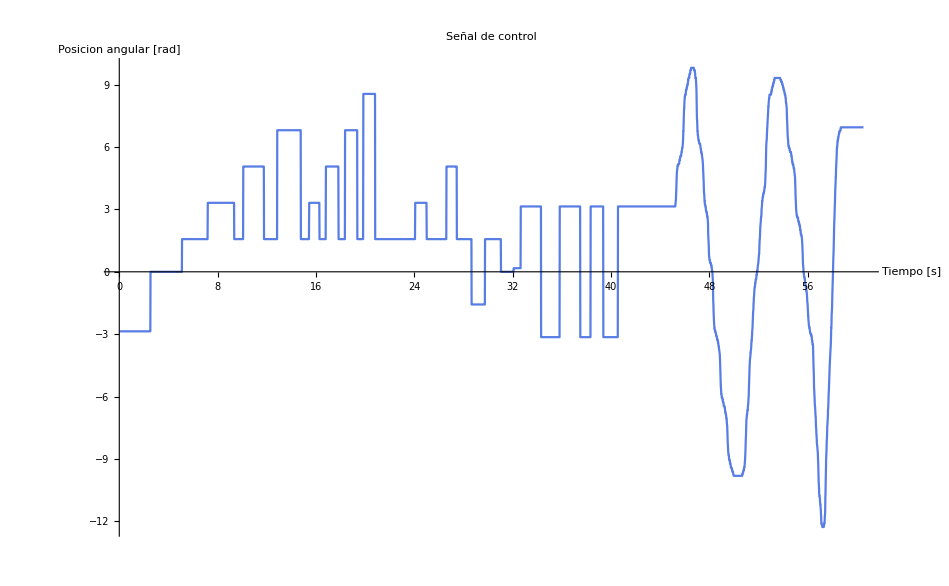

```mathematica
Ubicacion="C:\\Users\\Rodrigo\\Desktop\\Tesis\\DAQ\\Datos_Para_Entrenamiento\\Genomas\\Validacion";
SetDirectory[Ubicacion];
SeñalControl=Import["ControlSignal.csv","Data"];
GSC=ListLinePlot[SeñalControl,
PlotLabel->"Señal de control",
AxesLabel->{"Tiempo [s]","Posicion angular [rad]"},
PlotStyle->ColoresTema[[1]]
]
τ=Median[Differences[SeñalControl[[;;,1]]]];
RespuestaMotor=Import["MotorReactionToControlP.csv","Data"];
ListLinePlot[RespuestaMotor];
Export["ControlSignal.eps",GSC];
```

```mathematica
kv=0.031;k=0.031; Ra=0.27; La=0.4 10^-3; d=1.21 10^-5; J=2.61 10^-5*9.81;
Eq1=kv ωp[t]==−Ra ia[t]−La ia'[t]+Vt[t]
Eq2=k ia[t]==J ωp'[t]+d ωp[t]
Eq3=D[Eq2,t]
```

0.031 ωp[t]==-0.27 ia[t]+Vt[t]-0.0004 ia'[t]

0.031 ia[t]==0.0000121 ωp[t]+0.000256041 ωp'[t]

0.031 ia'[t]==0.0000121 ωp'[t]+0.000256041 ωp''[t]

```mathematica
Am=({{-Ra/La, -kv/La, 0}, {k/J, -d/J, 0}, {0, 1, 0}});Bm=({{1/La}, {0}, {0}}); Cm=({{0, 0, 1}});Dm={{0}};
Motor=StateSpaceModel[{Am,Bm,Cm,Dm}]
DMotor=ToDiscreteTimeModel[Motor,τ,"ZeroOrderHold"]
```

-675.-77.502500.121.074-0.04725810001000010StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNoneAutomatic

-0.703369-0.1766350.370.7890.2759480.8349550.344.9350.002121010.0141041.2.651260.00001630270.0001084070.01537260.02037830.0153726StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNoneAutomatic

```mathematica
ControlP=TransferFunctionModel[1,s];
Saturation=NonlinearStateSpaceModel[{0,9Clip[u]},x,u];
n=SystemsModelSeriesConnect[ControlP,Saturation];
n=SystemsModelSeriesConnect[n,Motor];
n=SystemsModelFeedbackConnect[n];
```

```mathematica
nd=ToDiscreteTimeModel[n,τ];
```

```mathematica
csdo=OutputResponse[nd,SeñalControl[[;;,2]]]//Flatten;
Error=Table[{RespuestaMotor[[i,1]],RespuestaMotor[[i,2]]-csdo[[i]]},{i,1,3821}];
ErrorRelativo=Table[Abs[RespuestaMotor[[i,2]]-csdo[[i]]]/RespuestaMotor[[i,2]],{i,1,3821}];
dm=8;
JFPE=(1+dm/3821)/(1-dm/3821)Sum[1/2 Error[[i,2]]^2,{i,3821}] 1/3821;

CompG=ListLinePlot[{RespuestaMotor,Table[{RespuestaMotor[[i,1]],csdo[[i]]},{i,1,3821}]},
FrameLabel->{"Tiempo [s]","Posicion angular [rad]"},
PlotStyle->ColoresTema[[1;;2]],
PlotLegends->{"Motor","Modelo"},
PlotLabel->Style["Comportamiento modelo clasico
FPE="<>ToString[JFPE,TraditionalForm],FontSize->20],
Frame->True(*,
PlotRange->All*)
];

ErrorG=ListLinePlot[Error,
PlotStyle->ColoresTema[[3]],
PlotLegends->"Error",
PlotRange->{-4,4},
FrameLabel->{"Tiempo [s]","Posicion angular [rad]"},
Frame->True];

GCM=Column[{
Show[CompG,ImagePadding->40,ImageSize->Large],
Show[ErrorG,ImagePadding->40,ImageSize->Large](*,
Style["Error Absoluto Maximo: "<>ToString[Max[Abs[Error[[;;,2]]]]]<>"
Error Absoluto Promedio: "<>ToString[Median[Abs[Error[[;;,2]]]]]<>"
Desviacion Estandar: "<>ToString[StandardDeviation[Abs[Error[[;;,2]]]]]<>"
Error Relativo Maximo: "<>ToString[Max[Abs[ErrorRelativo]]]<>"
Error Relativo Promedio: "<>ToString[Median[Abs[ErrorRelativo]]]<>"
FPE: "<>ToString[JFPE],TextAlignment->Left]*)},
Alignment->{Left,Right,Automatic}
]
(*Show[CompG,ErrorG,PlotRange->{{34,35},{-5,5}}]*)
Export["ComportamientoModeloClasico.eps",GCM];
```

Part::take: Cannot take positions 1 through 2 in ColoresTema.

ListLinePlot::prng: Value of option PlotRange -> {{0,60.5503},{-1.35743058515746×10^3671,1.24315765257035×10^3672}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Part::partd: Part specification ColoresTema⟦3⟧ is longer than depth of object.

## Validación

```mathematica
FPE={"FPE"};
EAM={"Error absoluto máximo"};
EAP={"Error absoluto promedio"};
DE={"Desviación Estandar"};
ERM={"Error relativo máximo"};
ERP={"Error relativo promedio"};

For[j=2,j<=Length[Files],j++,
csdo=Import[Files[[j]]<>"_val.csv","Data"][[;;,2]];

Error=Table[{RespuestaMotor[[i,1]],RespuestaMotor[[i,2]]-csdo[[i]]},{i,1,3821}];
ErrorRelativo=Table[Abs[RespuestaMotor[[i,2]]-csdo[[i]]]/RespuestaMotor[[i,2]],{i,1,3821}];
dm=Complejidad[[j]];
JFPE=(1+(dm/3821))/(1-(dm/3821))Sum[1/2 Error[[i,2]]^2,{i,3821}] 1/3821;

EAM=Join[EAM,{Max[Abs[Error[[;;,2]]]]}];
EAP=Join[EAP,{Median[Abs[Error[[;;,2]]]]}];
DE=Join[DE,{StandardDeviation[Abs[Error[[;;,2]]]]}];
ERM=Join[ERM,{Max[Abs[ErrorRelativo]]}];
ERP=Join[ERP,{Median[Abs[ErrorRelativo]]}];;
FPE=Join[FPE,{JFPE}];

CompG=ListLinePlot[{RespuestaMotor,Table[{RespuestaMotor[[i,1]],csdo[[i]]},{i,1,3821}]},
FrameLabel->{"Tiempo [s]","Posicion angular [rad]"},
PlotLegends->{"Motor","Red"},
PlotStyle->ColoresTema[[1;;2]],
PlotLabel->Column[{Trainings[[j]]<>"\n FPE="<>ToString[JFPE,TraditionalForm]},Center,ItemSize->CLS],
Frame->True,
PlotRange->Full
];

ErrorG=ListLinePlot[Error,
PlotStyle->ColoresTema[[3]],
PlotLegends->"Error",
PlotRange->{-4,4},
FrameLabel->{"Tiempo [s]","Posicion angular [rad]"},
Frame->True];

GCM=Column[{
Show[CompG,ImagePadding->{{40,10},{Automatic,20}},ImageSize->CIS],
Show[ErrorG,ImagePadding->{{40,10},{Automatic,20}},ImageSize->CIS](*,
Style["Error Absoluto Maximo: "<>ToString[EAM[[j]],TraditionalForm]<>"
Error Absoluto Promedio: "<>ToString[EAP[[j]],TraditionalForm]<>"
Desviacion Estandar: "<>ToString[DE[[j]],TraditionalForm]<>"
Error Relativo Maximo: "<>ToString[ERM[[j]],TraditionalForm]<>"
Error Relativo Promedio: "<>ToString[ERP[[j]],TraditionalForm]<>"
FPE: "<>ToString[JFPE,TraditionalForm],TextAlignment->Left]},
Alignment->{Left,Right,Automatic*)}
];
Export[Files[[j]]<>".eps",GCM];
(*Print[GCM]*)
];
```

## Gráficas Comparativas

```mathematica
BestNormFitness=BestFitness/MaxFitnessPosible 100/.{(" Aptitud ")/(" Aptitud máxima posible ")100->"Aptitud (%)"};
TablaComparativa=Grid[{Trainings,TotalDataPoints,NGen,MaxFitnessPosible,BestFitness,BestNormFitness ,ErrorTotal,Complejidad,EAM,EAP,DE,ERM,ERP,FPE}ᵀ,
ItemSize->{{25,8,Automatic,8,Automatic,6,Automatic,Automatic,8,8,8,8,8}},
Alignment->{Center,Center},
Frame->{None,All},
ItemStyle->Directive[TextAlignment->Center]
];
```

```mathematica
Insert[TablaComparativa,{Background->{None,{GrayLevel[0.7],{White}}},Dividers->{Black,{2->Black}},Frame->True,Spacings->{2,{2,{0.7},2}}},2]
Export["TablaTotal.eps",TablaComparativa]
```

Entrenamiento |  Datos totales  |  Generaciones  |  Aptitud máxima posible  |  Aptitud  | Aptitud (%) |  EAA(Entrenamiento)  | Complejidad | Error absoluto máximo | Error absoluto promedio | Desviación Estandar | Error relativo máximo | Error relativo promedio | FPE
Chirp 1  | 10000 | 249 | 3.13651×10^6 | 2.18474×10^6 | 69.655 | 590406. | 7 | 133.594 | 118.09 | 14.0411 | 15813.2 | 37.0466 | 6822.57
Chirp 1, Chirp 2, Chirp 3, Chirp 4, Chirp 5  | 50000 | 83 | 7.20478×10^7 | 5.15794×10^7 | 71.5905 | 2.77559×10^6 | 16 | 714.917 | 700.859 | 19.7124 | 91605.8 | 219.735 | 247421.
Chirp 1, Chirp 2, Chirp 3, Chirp 4, Chirp 5  40m | 50000 | 731 | 7.20478×10^7 | 5.35353×10^7 | 74.3052 | 2.91889×10^6 | 18 | 522.073 | 414.414 | 35.0928 | 54009. | 131.956 | 92326.4
Chirp 1, Chirp 4, Chirp mr 1, Chirp mr 5  | 22000 | 120 | 2.63332×10^7 | 2.58463×10^7 | 98.1512 | 111157. | 5 | 23.6715 | 7.38595 | 3.39947 | 1122.62 | 2.34701 | 42.4649
Chirp 1, Chirp 4, Chirp mr 1, Chirp mr 5, PRB mr 1, PRB mr 2  | 24000 | 154 | 2.9302×10^7 | 2.77782×10^7 | 94.7995 | 126615. | 6 | 12.0432 | 2.58127 | 1.79445 | 192.502 | 0.806325 | 5.54121
Chirp 1, Chirp 4, Chirp mr 3, Impulso 1, PRB 1, PRB 4, PRB mr 2  | 43000 | 102 | 8.57378×10^7 | 8.28352×10^7 | 96.6145 | 172565. | 8 | 10.5929 | 1.86613 | 1.52536 | 170.562 | 0.596279 | 3.51991
Chirp 1, Chirp mr 1, Chirp 2, PRB mr 1  | 22000 | 149 | 1.27135×10^7 | 8.54131×10^6 | 67.1828 | 1.10478×10^6 | 21 | 609.608 | 338.038 | 47.84 | 49321.7 | 107.493 | 61288.7
Chirp 1  40m | 10000 | 3462 | 3.13651×10^6 | 3.06156×10^6 | 97.6104 | 48594.3 | 27 | 16.1442 | 0.842612 | 2.05452 | 880.92 | 0.287534 | 3.64692
Chirp 2  | 10000 | 457 | 8.37867×10^6 | 8.30778×10^6 | 99.154 | 41928.4 | 18 | 37.5286 | 15.6626 | 6.32054 | 1691.81 | 5.18504 | 159.283
Chirp 2, Chirp 4, Chirp mr 5, Chirp mr 1, PRB 1, PRB 2, PRB 3, PRB 4, PRB 5, PRB 6, PRB mr 1  | 83000 | 88 | 2.26049×10^8 | 1.80989×10^8 | 80.0662 | 2.43534×10^6 | 14 | 573.547 | 557.969 | 28.7896 | 73266.6 | 175.686 | 153297.
Chirp 3  | 10000 | 459 | 1.4289×10^7 | 1.33448×10^7 | 93.3921 | 525451. | 11 | 690.772 | 675.311 | 88.6368 | 88463.4 | 211.855 | 217225.
Chirp 4  | 10000 | 418 | 2.01819×10^7 | 1.92477×10^7 | 95.3707 | 496631. | 10 | 906.119 | 883.811 | 183.758 | 115540. | 278.988 | 334108.
Chirp 5  | 10000 | 442 | 2.60616×10^7 | 2.50154×10^7 | 95.9854 | 555760. | 19 | 1269.04 | 1253.39 | 177.571 | 163836. | 393.222 | 741323.
Chirp 5, Chirp mr 1, PRB 5  | 21000 | 186 | 9.15934×10^7 | 7.04711×10^7 | 76.939 | 1.81655×10^7 | 21 | 1591.56 | 631.031 | 127.457 | 77261.1 | 200.249 | 212798.
Chirp 5  40m | 10000 | 2124 | 2.60616×10^7 | 2.57049×10^7 | 98.631 | 260040. | 21 | 46630.8 | 38064.9 | 12185.1 | 5.03559×10^6 | 12515.7 | 6.42327×10^8
Chirp mr 1  | 1000 | 3263 | 355963. | 353418. | 99.285 | 1514.3 | 28 | 68.0623 | 43.8034 | 17.6789 | 6674.22 | 11.8235 | 855.286
Chirp mr 1, Chirp mr 2, Chirp mr 3, Chirp mr 4, Chirp mr 5  | 5000 | 720 | 7.45002×10^6 | 7.43183×10^6 | 99.7558 | 3150.68 | 20 | 3.98154 | 0.126692 | 0.50282 | 69.0146 | 0.0421141 | 0.18249
Chirp mr 1, Chirp mr 2, Chirp mr 3, Chirp mr 4, Chirp mr 5, Impulso 1  | 6000 | 491 | 7.49353×10^6 | 7.37737×10^6 | 98.4498 | 3100.71 | 18 | 4.20431 | 0.231471 | 0.483629 | 99.6661 | 0.0831256 | 0.198652
Chirp mr 1, Chirp mr 2, Chirp mr 3, Chirp mr 4, Chirp mr 5, Impulso 1, PRB mr 1, PRB mr 2, tj Chirp 2, tj Chirp mr 1, tj Chirp mr 2, tj Chirp mr 3, tj PRB 2  | 42385 | 194 | 6.04492×10^7 | 2.47687×10^7 | 40.9744 | 50343.2 | 18 | 11.5554 | 3.91087 | 1.14073 | 654.173 | 1.22064 | 8.64573
Chirp mr 1, Chirp mr 2, Chirp mr 3, Chirp mr 4, Chirp mr 5, Impulso 1  40m | 6000 | 2944 | 7.49353×10^6 | 7.38913×10^6 | 98.6068 | 2672. | 20 | 4.31169 | 0.318818 | 0.474256 | 114.2 | 0.105741 | 0.222752
Chirp mr 1, Chirp mr 2, Chirp mr 3, Chirp mr 4, Chirp mr 5, PRB mr 1, PRB mr 2  | 7000 | 203 | 1.04189×10^7 | 1.01524×10^7 | 97.4425 | 104944. | 26 | 5.46353 | 0.328169 | 0.655834 | 84.4624 | 0.108249 | 0.360136
Chirp mr 1, Chirp mr 2, Chirp mr 3, Chirp mr 4, Chirp mr 5  40m | 5000 | 6363 | 7.45002×10^6 | 7.43267×10^6 | 99.7671 | 2594.25 | 26 | 3.72296 | 0.130325 | 0.473206 | 65.546 | 0.0429127 | 0.15946
Chirp mr 1, Chirp mr 2, PRB mr 2  | 3000 | 1451 | 3.36735×10^6 | 3.29929×10^6 | 97.979 | 28342.7 | 25 | 3.88161 | 0.255014 | 0.523069 | 118.206 | 0.0869043 | 0.230173
Chirp mr 2  | 1000 | 2427 | 884907. | 883143. | 99.8006 | 1087.51 | 23 | 5.60088 | 0.371633 | 0.783724 | 62.0579 | 0.137107 | 0.544928
Chirp mr 3  | 1000 | 2824 | 2.07068×10^6 | 2.06721×10^6 | 99.8323 | 2883.42 | 22 | 3.46427 | 0.617127 | 0.351719 | 29.2982 | 0.207268 | 0.291813
Chirp mr 4  | 1000 | 2818 | 1.47972×10^6 | 1.47812×10^6 | 99.8921 | 1062.87 | 11 | 3.90759 | 0.249852 | 0.486856 | 51.4218 | 0.0785037 | 0.198516
Chirp mr 4  40m | 1000 | 20360 | 1.47972×10^6 | 1.47818×10^6 | 99.8963 | 993.841 | 34 | 3.57757 | 0.333948 | 0.365572 | 40.9228 | 0.113887 | 0.15607
Chirp mr 5  | 1000 | 2392 | 2.65875×10^6 | 2.65607×10^6 | 99.8991 | 2009.3 | 27 | 3.37898 | 1.05187 | 0.255681 | 116.499 | 0.343296 | 0.600232
Impulso 1  | 1000 | 2827 | 43509.8 | 36544.6 | 83.9916 | 1295.36 | 32 | 77.4175 | 9.65812 | 26.4959 | 7880.32 | 4.58461 | 682.385
PRB 10  | 20000 | 385 | 6.48443×10^7 | 5.35358×10^7 | 82.5606 | 2.80479×10^6 | 12 | 3058.74 | 3049.39 | 273.923 | 397376. | 957.02 | 4.5635×10^6
PRB 1  | 10000 | 351 | 7.44651×10^6 | 6.61925×10^6 | 88.8906 | 530002. | 13 | 221.235 | 96.3697 | 62.426 | 13130.2 | 33.0234 | 6981.
PRB 2  | 10000 | 380 | 2.17608×10^7 | 1.87851×10^7 | 86.3252 | 2.38914×10^6 | 35 | 1053.75 | 1037.78 | 42.4572 | 135616. | 325.86 | 546701.
PRB 3  | 10000 | 397 | 3.62688×10^7 | 3.40711×10^7 | 93.9404 | 1.63076×10^6 | 25 | 3782.89 | 2599.91 | 1057.48 | 347018. | 880.701 | 3.36721×10^6
PRB 4  | 10000 | 318 | 5.07322×10^7 | 4.7446×10^7 | 93.5225 | 2.37722×10^6 | 24 | 2507.4 | 2491.9 | 79.3919 | 325309. | 782.876 | 3.13771×10^6
PRB 5  | 10000 | 274 | 6.51758×10^7 | 6.45651×10^7 | 99.063 | 290807. | 5 | 2197.08 | 1055.54 | 626.115 | 143009. | 370.048 | 767351.
PRB 6  | 10000 | 382 | 1.22473×10^7 | 8.54466×10^6 | 69.7676 | 3.10226×10^6 | 7 | 775.48 | 766.249 | 64.1838 | 99680.9 | 240.851 | 288609.
PRB 7  | 10000 | 468 | 2.39132×10^7 | 2.33782×10^7 | 97.7627 | 411292. | 25 | 225.822 | 128.331 | 54.2695 | 16967.3 | 44.6024 | 9589.35
PRB 7  40m | 10000 | 3354 | 2.39132×10^7 | 2.33431×10^7 | 97.6161 | 324842. | 21 | 244390. | 123839. | 70128.9 | 1.67815×10^7 | 43127.1 | 1.01374×10^10
PRB 8  | 10000 | 614 | 3.5056×10^7 | 3.23396×10^7 | 92.2513 | 1.98749×10^6 | 34 | 1989.85 | 1702.9 | 516.658 | 224392. | 558.584 | 1.26849×10^6
PRB 8  40m | 10000 | 3653 | 3.5056×10^7 | 3.41467×10^7 | 97.4061 | 548576. | 26 | 953.835 | 944.556 | 31.4266 | 122925. | 297.201 | 450716.
PRB 9  | 10000 | 464 | 4.6211×10^7 | 4.5682×10^7 | 98.8553 | 297038. | 11 | 10.3266 | 1.62976 | 1.55035 | 165.617 | 0.511537 | 3.31681
PRB 9, PRB 10, PRB 1, PRB 2, PRB 3, PRB 4, PRB 5, PRB 6  | 90000 | 95 | 3.04687×10^8 | 1.51211×10^8 | 49.6283 | 1.27781×10^7 | 22 | 693.773 | 677.561 | 19.4065 | 88654.8 | 212.719 | 232209.
PRB mr 1  | 1000 | 3764 | 842396. | 823827. | 97.7957 | 10936.4 | 25 | 15.1772 | 2.29779 | 2.29191 | 266.498 | 0.741407 | 6.70729
PRB mr 1, PRB mr 2  | 2000 | 2156 | 2.96887×10^6 | 2.92569×10^6 | 98.5457 | 13430.7 | 24 | 13.6658 | 1.95223 | 2.06745 | 443.478 | 0.631138 | 5.29552
PRB mr 2  | 1000 | 3531 | 2.12647×10^6 | 2.09271×10^6 | 98.4122 | 15045.6 | 40 | 725.934 | 12.2655 | 114.722 | 10602. | 3.36616 | 7459.6
tj Chirp 2  | 14984 | 1156 | 1.25622×10^7 | 5.28296×10^6 | 42.0545 | 2.06857×10^6 | 1 | 16.9706 | 3.08966 | 3.21456 | 759.536 | 1.41405 | 12.5973
tj Chirp 2, tj Chirp mr 1, tj Chirp mr 2, tj Chirp mr 3  | 19447 | 577 | 1.74872×10^7 | 4.92679×10^6 | 28.1737 | 340264. | 15 | 383.83 | 368.326 | 35.9888 | 48438.9 | 115.549 | 66256.2
tj Chirp mr 1  | 1491 | 8814 | 534013. | 287229. | 53.7869 | 89028.5 | 1 | 12.3033 | 3.19642 | 2.61803 | 1.707 | 1.00398 | 10.1713
tj Chirp mr 2  | 1493 | 8909 | 1.32733×10^6 | 808250. | 60.8929 | 3085.12 | 36 | 5.39298 | 0.273057 | 0.439453 | 67.3909 | 0.0883417 | 0.174128
tj Chirp mr 2  40m | 1493 | 32310 | 1.32733×10^6 | 433206. | 32.6374 | 2485.26 | 50 | 14.2222 | 7.8332 | 3.61941 | 881.318 | 2.17531 | 32.5447
 Chirp mr 1,  Chirp mr 2,  Chirp mr 3,  Chirp mr 4,  Chirp mr 5 30m seed | 5000 | 4797 | 7.45002×10^6 | 7.43886×10^6 | 99.8501 | 1486.07 | 29 | 5.26745 | 0.146785 | 0.537647 | 70.8157 | 0.0491924 | 0.208764
 Chirp mr 4 30m seed | 1000 | 13715 | 1.47972×10^6 | 1.47824×10^6 | 99.9 | 981.727+Abs[Error] | 13 | 3.2751 | 0.274019 | 0.375056 | 30.0898 | 0.093907 | 0.136428

TablaTotal.eps

```mathematica
CorrelationTest[{NGen[[2;;]],TotalDataPoints[[2;;]]}ᵀ]
CorrelationTest[{NGen[[2;;]],BestNormFitness[[2;;]]}ᵀ]
CorrelationTest[{NGen[[2;;]],FPE[[2;;]]}ᵀ]
```

2.41416×10^-13

0.00341398

0.00104927

## Pruebas

```mathematica
Files//MA
```

```mathematica
SystemsModelSeriesConnect[ControlP,(9Clip[#1])&]
LaplaceTransform[9Clip[x[t]],t,s]
```

SystemsModelSeriesConnect[1TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11111FalseFalseFalseAutomaticNoneAutomatic,9 Clip[#1]&]

9 LaplaceTransform[Clip[x[t]],t,s]

```mathematica
Clip[1,{-9,9}]
ControlP
```

1

1TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11111FalseFalseFalseAutomaticNoneAutomatic

```mathematica
-3
```

-3.

09 Clip[u]x 1111NoneNoneFalseFalseFalse{u}Automatic